# A Simple Inverse Cellular Automata for Biological Evolution

User-entered Parameters

Target Lifetime lifetime to which an adaptive mutation chain should reach
Rule Bucket size number of adaptive mutation chain iterations
Max Mutation Attempts per iteration
Debug Flag

Successful Scenario of an Adaptive Mutation Chain

Lifetime reached = Target lifetime
Rule progression is plotted
Iterations per lifetime table is printed

Failed Scenarios of an Adaptive Mutation Chain

Lifetime reached > Target lifetime
Lifetime reached < Target lifetime after all unique point mutations fail
Maximum mutation attempts per iteration exceeded

Point mutation chains are run using  WL  functions RandomRuleMutation and TestLifetime

```mathematica
TestLifetime[rule_,init_List:{1},
max_Integer:100(*,infinity_:Infinity*)]:=With[
{array=CellularAutomaton[rule,{init,0},{max,All}]},If[#==0,-Infinity(*-infinity*),max-#+1]&[
LengthWhile[Reverse[array],Total[#]==0&]
]
]

RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]

RuleMutationsList[{rn_,k_,r_},many_Integer:1,OptionsPattern[{"Symmetric"->False}]]:=Module[{up,down,cases},{up,down}=If[TrueQ[OptionValue["Symmetric"]],{SymUp[k,r],SymDown[k,r]},{All,All}];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
Catenate[Outer[Function[{sels,vals},{FromDigits[#[[up]],k],k,r}&[Fold[Function[{res,it},MapAt[Mod[#+it[[2]],k]&,res,it[[1]]]],cases,Transpose[{sels,vals}]]]],Subsets[Range[1,Length[cases]-1],{many}],Tuples[Range[1,k-1],many],1]]]

CustomStyleData[key_]:=Lookup[
Association[
"Colors"->{
0->White,1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]
},
"HighlightColors"->{
0->White,-1->Hue[0.06, 1, 1],-2->Hue[0.73, 1, 1],1->Lighter[Hue[0.06, 1, 1],0.8],2->Lighter[Hue[0.73, 1, 1],0.8]
},
"Landscape"->{Hue[0.58, 1., 0.76],Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},
"ListPlot"->Directive[RGBColor[0.368417, 0.506779, 0.709798],EdgeStyle[Opacity[0.25]]]
],
Key[key]
]
```

searchForUnfitRules simply creates a random set of rules which are constraint to a lifetime of 1 which are the ones we want to start the point mutations chains from - this is ensured when the four relevant neighbourhoods for the fixed initial condition transform to zero by the rule, hence we are fixing {0, 0, 0}→0, {0, 0, 1}→0, {0, 1, 0}→0 and {1, 0, 0}→0 (for which the least significant ternary bits are {27,26,24,18})

```mathematica
ClearAll[searchForUnfitRules]

searchForUnfitRules[sampleSize_ : 1000,k_ : 3]:=
    Module[{rules,fixedPositions},
      fixedPositions={27,26,24,18};
      
      rules=Sort[
        DeleteDuplicates[
          Table[
            FromDigits[
              ReplacePart[RandomInteger[{0,k-1},27],
                Thread[fixedPositions->0]],k
            ],
            {sampleSize}
          ]
        ]
      ];
      
    Return[rules];
    ]
```

Main code, explanatory comments inline

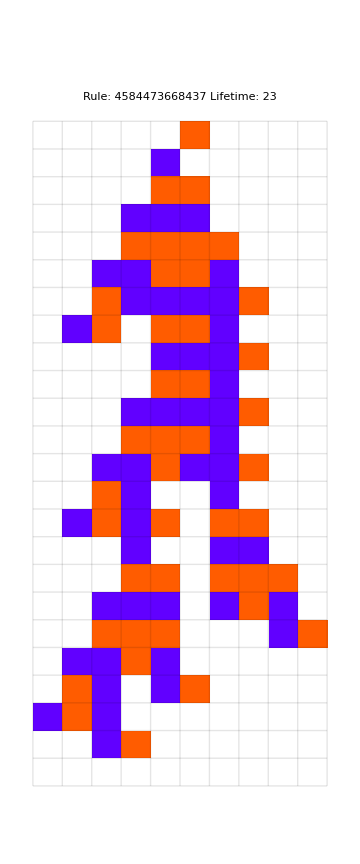
-Graphics-Lifetime | Iterations
1 | 449
2 | 126
3 | 69
5 | 19
6 | 74
9 | 14
12 | 5
15 | 3
16 | 1
18 | 1
21 | 2
23 | 1

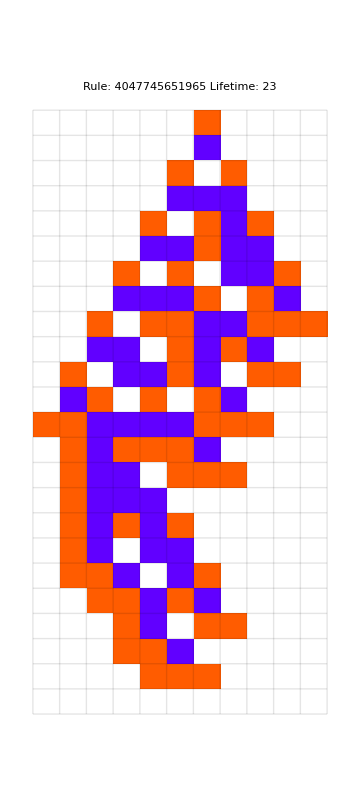
-Graphics-Lifetime | Iterations
1 | 296
3 | 141
4 | 26
5 | 35
8 | 9
9 | 7
10 | 1
11 | 1
20 | 1
21 | 2
23 | 1

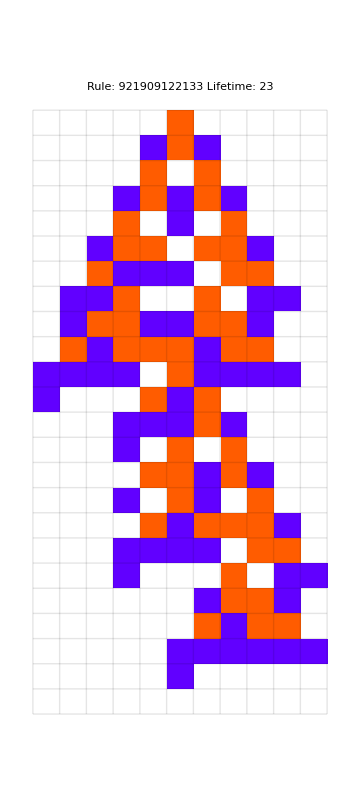
-Graphics-Lifetime | Iterations
1 | 34
2 | 17
4 | 16
5 | 30
6 | 27
7 | 31
8 | 3
11 | 2
12 | 2
15 | 1
18 | 1
20 | 1
23 | 1

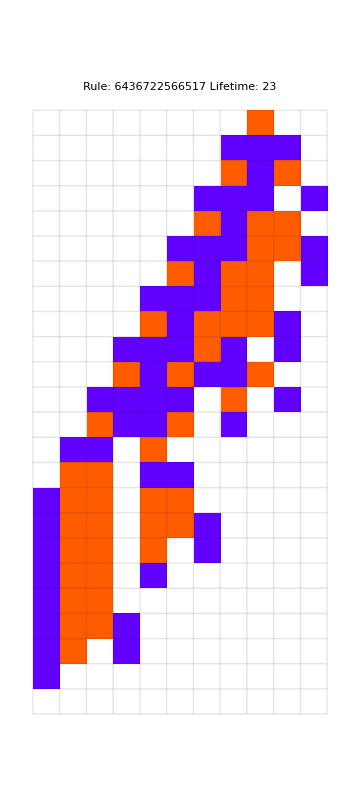
-Graphics-Lifetime | Iterations
1 | 273
2 | 21
3 | 4
6 | 1
10 | 3
11 | 7
17 | 14
21 | 3
23 | 1

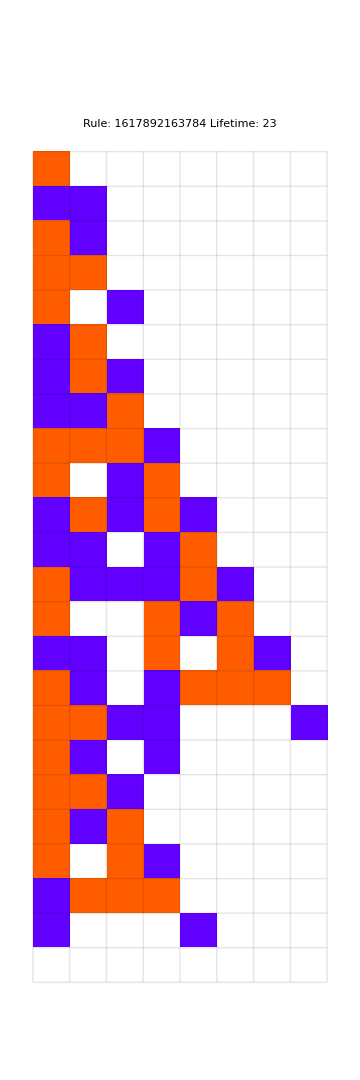
-Graphics-Lifetime | Iterations
1 | 387
2 | 3
3 | 40
4 | 23
5 | 52
8 | 11
11 | 19
18 | 1
23 | 1

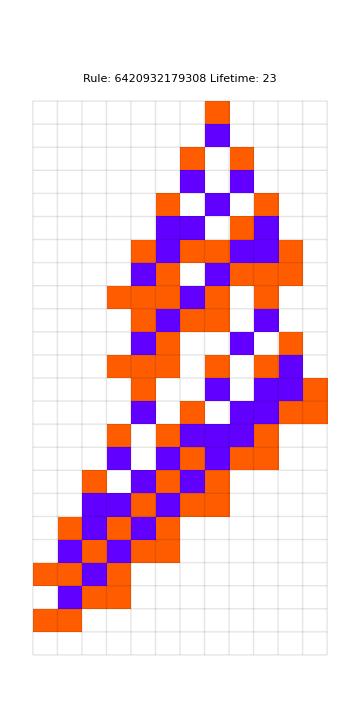
-Graphics-Lifetime | Iterations
1 | 188
3 | 122
4 | 43
5 | 1
7 | 12
12 | 6
15 | 9
18 | 2
23 | 1

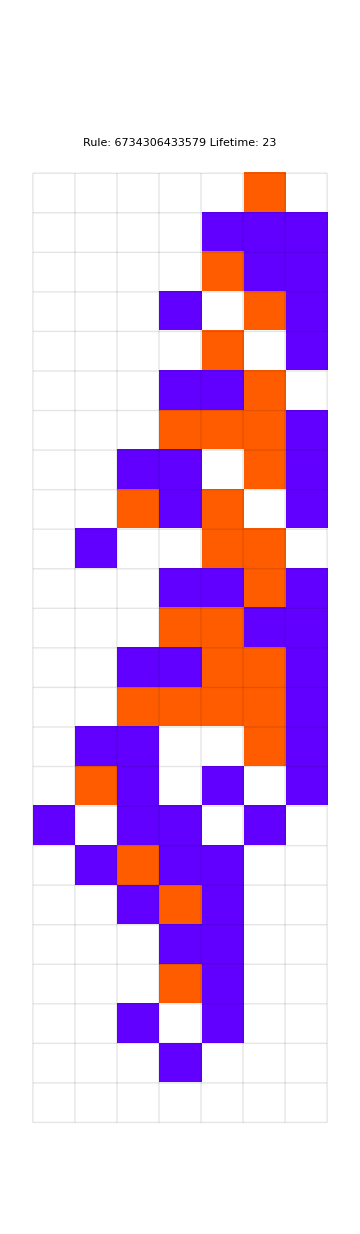
-Graphics-Lifetime | Iterations
1 | 440
2 | 73
3 | 5
4 | 3
5 | 3
6 | 1
7 | 3
8 | 12
9 | 2
16 | 10
21 | 1
23 | 1

Summary | 
Target Lifetime | 23
Number Of Mutation Chains | 46
Number Of Successful Mutation Chains | 7
Max Mutation Attempts Per Chain | 7000
Debug Flag | False

```mathematica
Module[
  {maxLifetime=200,originalRule,mutatedRule,originalLifetime,mutatedLifetime,data,k=3,lifetimeCounter=<||>,ruleSerialNumber,progressIndicator, ruleMutations,mutationsAttemptsPerRule,mutationSet, successfulChains=0},

(*Create a dialog to prompt the user for input and validate input to be positive integers*){targetLifetime,maxMutationsAttemptsPerRule,ruleBucketSize,debugFlag}=DialogInput[DynamicModule[{targetLifetime=20,maxMutationsAttemptsPerRule=500,ruleBucketSize=10,debugFlag=False},Column[{Style["Configuration (enter positive integers)",FontSize->18],
Row[{"Target Lifetime ",InputField[Dynamic[targetLifetime],Number,FieldSize->Tiny]}],Row[{"Number Of Mutation Chains ",InputField[Dynamic[ruleBucketSize],Number,FieldSize->Tiny]}],Row[{"Max Mutation Attempts Per Chain ",InputField[Dynamic[maxMutationsAttemptsPerRule],Number,FieldSize->Tiny]}],Row[{"Debug Flag ",PopupMenu[Dynamic[debugFlag],{True,False}]}],DefaultButton["OK",DialogReturn[If[And@@(IntegerQ/@{targetLifetime,maxMutationsAttemptsPerRule,ruleBucketSize})&&And@@(Positive/@{targetLifetime,maxMutationsAttemptsPerRule,ruleBucketSize}),{targetLifetime,maxMutationsAttemptsPerRule,ruleBucketSize,debugFlag},{Null,Null,Null,Null} (*Return a list of Nulls instead of DialogReturn[{}]*)]]]}]]];

(*Check if inputs are valid*)
If[MemberQ[{targetLifetime,maxMutationsAttemptsPerRule,ruleBucketSize},Null],Return["Invalid input. Please enter positive integers for all fields."]];

(* Call searchForUnfitRules and store the result in RuleBucket which contains a list of rules with a lifetime of 1 *)    RuleBucket=searchForUnfitRules[ruleBucketSize];

(*Initialize the progress indicator*)
 ruleSerialNumber=0;
 progressIndicator=ProgressIndicator[Dynamic[ruleSerialNumber/ruleBucketSize],{0,1}];
 Print[progressIndicator];

  (* Iterate over each rule in RuleBucket *)
  Do[
    
 ruleSerialNumber++;

(*Update progress indicator*)
Pause[0.1];
 
(* Print summary of run when it is done *)
If[ruleSerialNumber==ruleBucketSize,
	Print[
		Grid[
			{
				{"Summary",""},
				{"Target Lifetime",targetLifetime},
				{"Number Of Mutation Chains",ruleBucketSize},
				{"Number Of Successful Mutation Chains",successfulChains},
				{"Max Mutation Attempts Per Chain",maxMutationsAttemptsPerRule},
				{"Debug Flag",debugFlag}
			},
			Frame->All,
			Background->{None,{LightGray,{White}}},
			ItemStyle->Directive[Bold,FontColor->Darker[Red]],
			Spacings->{2,2},
			Alignment->Center
		]
	];
  ];

    mutationsAttemptsPerRule=0;
    lifetimeCounter=<||>;
    originalRule=rule;
    originalLifetime=1;
    lifetimeCounter[originalLifetime]=1;

    (* Continuously attempt mutations *)
    While[mutationsAttemptsPerRule<maxMutationsAttemptsPerRule,
      mutationSet=<||>;
      ruleMutations=0;

      While[ruleMutations<52, (* a max of 52 point mutations per rule *)
        (* Attempt a new point mutation *)
        mutatedRule=RandomRuleMutation[{originalRule,k,1}];
        mutationsAttemptsPerRule++;

        (* Avoid repeating mutations *)
        If[!KeyExistsQ[mutationSet,mutatedRule],
          mutationSet[mutatedRule]=True;
          ruleMutations++;

          (* Test the lifetime of the mutated rule *)
          mutatedLifetime=TestLifetime[mutatedRule,maxLifetime];

          (*
          Print["Rule: ",First[mutatedRule]," ruleMutations: ",ruleMutations," totMutations: ", mutationsAttemptsPerRule," Lifetime: ",mutatedLifetime];
          *)

          If[mutationsAttemptsPerRule==maxMutationsAttemptsPerRule,
            If[debugFlag==True,
              Print["REACHED MAXIMUM MUTATIONS PER RULE! Last Rule Number: ",originalRule," Last Lifetime: ",originalLifetime ];
            ];
          ];

          (* Check if the mutated rule's lifetime is equal to or greater than the current lifetime, if so then accept mutation*)
          If[
            mutatedLifetime>=originalLifetime,
            (* Update the rule and its lifetime *)
            originalRule=First[mutatedRule];
            originalLifetime=mutatedLifetime;

            (* Update the counter for the new lifetime *)
            If[KeyExistsQ[lifetimeCounter,originalLifetime],
              lifetimeCounter[originalLifetime]++,
              lifetimeCounter[originalLifetime]=1
            ];

            (* Break to check lifetime reached and start mutating the accepted rule again if necessary *)
            Break[]
          ];
        ]
      ];

      (* If the lifetime reached exceeded the lifetime target, move to the next rule from ruleBucket *)
       If[originalLifetime>targetLifetime,
        If[debugFlag==True,
          Print["EXCEEDED TARGET! Last Rule Number: ",originalRule," Last Lifetime: ",originalLifetime ];
        ];
        Break[]
      ];

      (* If the exact lifetime target was reached, plot and move to the next rule from ruleBucket *)
      If[originalLifetime==targetLifetime,

        If[debugFlag==True,
          Print["SUCCESS! Last Rule Number: ",originalRule," Last Lifetime: ",originalLifetime ];
        ];

	successfulChains++;

	data=CellularAutomaton[{originalRule,k,1},{{1},0},originalLifetime];
	
	Print[Row[
	  {
	    ArrayPlot[
	      data,
	      PlotLabel->Row[{"Rule: ",originalRule,"   Lifetime: ",originalLifetime}],
	      ImageSize->Medium,
	      ColorRules->CustomStyleData["Colors"],
	      Mesh->True,
	      MeshStyle->Opacity[.1]
	    ],
	    Spacer[50],
	    Grid[
	      {{"Lifetime","Iterations"}} ~Join~ SortBy[Normal[KeyValueMap[List,lifetimeCounter]],First],
	      Frame->All,
	      Background->{None,{LightGray,{White}}},
	      Spacings->{2,2},
	      Alignment->Center,
	      ItemStyle->Directive[Bold,FontColor->Darker[Blue]]
	    ]
	  }
	]];

        Break[]
      ];

      (* If no successful mutations are found, move to the next rule from ruleBucket *)
      If[ruleMutations>=52,
        If[debugFlag==True,
          Print["ALL 52 POINT MUTATIONS FAILED! Last Rule Number: ",originalRule," Last Lifetime: ",originalLifetime];
        ];
        Break[];
      ];
    ],
    {rule,RuleBucket}
  ]
]
```